GEOMETRICKÁ TRANSFORMÁCIA TROJUHOLNÍKA - ZLOŽITÁ ÚLOHA

==========================================

ZADANIE PRE ŠTUDENTA:

Majme trojuholník ABC s vrcholmi:

(3 | 1
1 | 4
-1 | 2)

Vykonajte postupne tieto transformácie:

1. Vykonajte symetriu trojuholníka v 2D priestore podľa priamky 3x -5y -1 = 0

2. Vykonajte skosenie trojuholníka v 2D priestore v smere osi x s koeficientom -3/2 a v smere osi y s koeficientom 1

3. Vykonajte zväčšenie v smere osi x s koeficientom 3/2 a zväčšenie v smere osi y s koeficientom 1 trojuholníka

RIEŠENIE:

GEOMETRICKÁ TRANSFORMÁCIA TROJUHOLNÍKA - ZLOŽITÁ ÚLOHA

==========================================

POČIATOČNÝ TROJUHOLNÍK:

Vrcholy trojuholníka ABC:

(3 | 1
1 | 4
-1 | 2)

Vlastnosti trojuholníka:

Obsah: 5

Obvod: 11

PRVÁ TRANSFORMÁCIA: Symetria

GEOMETRICKÉ TRANSFORMÁCIE TROJUHOLNÍKA - SYMETRIA

========================================

ZADANIE:

Majme trojuholník ABC s vrcholmi:

(3 | 1
1 | 4
-1 | 2)

Vykonajte symetriu v 2D priestore podľa priamky 3x - 5y - 1 = 0.

TEÓRIA MATICOVÉHO ZOBRAZENIA SYMETRIE:

Pri symetrii podľa priamky ax + by + c = 0 v 2D priestore môžeme použiť homogénnu transformačnú maticu 3×3:

Homogénna transformačná matica pre symetriu má tvar:

((b^2 - a^2)/(a^2 + b^2) | -2ab/(a^2 + b^2) | -2ac/(a^2 + b^2)
-2ab/(a^2 + b^2) | (a^2 - b^2)/(a^2 + b^2) | -2bc/(a^2 + b^2)
0 | 0 | 1)

Výhoda použitia homogénnej matice je, že zahŕňa lineárnu transformáciu aj posun v jednej matici, čo umožňuje

jednoduché reťazenie viacerých transformácií pomocou násobenia matíc.

VÝPOČET TRANSFORMAČNEJ MATICE PRE SYMETRIU:

Pre našu priamku 3x + -5y + -1 = 0:

Vypočítame jednotlivé prvky matice použitím vzorca:

Menovateľ: a.b2 + b.b2 = 3.b2 + -5.b2 = 34

Prvý riadok matice:

M[1,1] = (b.b2 - a.b2)/(a.b2 + b.b2) = (25 - 9)/(34) = 8/17

M[1,2] = -2ab/(a.b2 + b.b2) = -2·3·-5/(34) = 15/17

M[1,3] = -2ac/(a.b2 + b.b2) = -2·3·-1/(34) = 3/17

Druhý riadok matice:

M[2,1] = -2ab/(a.b2 + b.b2) = -2·3·-5/(34) = 15/17

M[2,2] = (a.b2 - b.b2)/(a.b2 + b.b2) = (9 - 25)/(34) = -8/17

M[2,3] = -2bc/(a.b2 + b.b2) = -2·-5·-1/(34) = -5/17

Tretí riadok matice:

M[3,1] = 0, M[3,2] = 0, M[3,3] = 1 (štandardné hodnoty pre homogénnu transformáciu)

VÝSLEDNÁ TRANSFORMAČNÁ MATICA:

(8/17 | 15/17 | 3/17
15/17 | -8/17 | -5/17
0 | 0 | 1)

Pre našu priamku 3x - 5y - 1 = 0:

a = 3

b = -5

c = -1

VÝPOČET SYMETRIE JEDNOTLIVÝCH VRCHOLOV:

VRCHOL A:

Pôvodné súradnice: [3, 1]

Výpočet pomocou homogénnej matice:

(8/17 | 15/17 | 3/17
15/17 | -8/17 | -5/17
0 | 0 | 1) |  ·  | (3
1
1) |  =  | (42/17
32/17
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (8/17 · 3) + (15/17 · 1) + (3/17 · 1)

= 24/17 + 15/17 + 3/17

= 42/17

• Výpočet novej y-ovej súradnice:

= (15/17 · 3) + (-8/17 · 1) + (-5/17 · 1)

= 45/17 + -8/17 + -5/17

= 32/17

Výsledná reprezentácia bodu A':

[42/17, 32/17]

--------------------------------------------------

VRCHOL B:

Pôvodné súradnice: [1, 4]

Výpočet pomocou homogénnej matice:

(8/17 | 15/17 | 3/17
15/17 | -8/17 | -5/17
0 | 0 | 1) |  ·  | (1
4
1) |  =  | (71/17
-22/17
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (8/17 · 1) + (15/17 · 4) + (3/17 · 1)

= 8/17 + 60/17 + 3/17

= 71/17

• Výpočet novej y-ovej súradnice:

= (15/17 · 1) + (-8/17 · 4) + (-5/17 · 1)

= 15/17 + -32/17 + -5/17

= -22/17

Výsledná reprezentácia bodu B':

[71/17, -22/17]

--------------------------------------------------

VRCHOL C:

Pôvodné súradnice: [-1, 2]

Výpočet pomocou homogénnej matice:

(8/17 | 15/17 | 3/17
15/17 | -8/17 | -5/17
0 | 0 | 1) |  ·  | (-1
2
1) |  =  | (25/17
-36/17
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (8/17 · -1) + (15/17 · 2) + (3/17 · 1)

= -8/17 + 30/17 + 3/17

= 25/17

• Výpočet novej y-ovej súradnice:

= (15/17 · -1) + (-8/17 · 2) + (-5/17 · 1)

= -15/17 + -16/17 + -5/17

= -36/17

Výsledná reprezentácia bodu C':

[25/17, -36/17]

--------------------------------------------------

ŠPECIÁLNE MATICE PRE NIEKTORÉ TYPY SYMETRIÍ:

POSTUP:

Pre výpočet osovej symetrie podľa priamky 3x - 5y - 1 = 0 používame vzorce:

Všeobecný vzorec pre výpočet symetrie bodu [x, y] podľa priamky ax + by + c = 0:

x' = x - 2a(ax + by + c)/(a.b2 + b.b2)

y' = y - 2b(ax + by + c)/(a.b2 + b.b2)

Tento vzorec môžeme zapísať v maticovej forme pomocou homogénnych súradníc [x, y, 1]

ako násobenie s 3×3 maticou, čo umožňuje jednoduché zreťazenie transformácií.

Naše hodnoty koeficientov:

a = 3

b = -5

c = -1

Rovnica osi symetrie: 3x - 5y - 1 = 0

Normálový vektor osi symetrie: (3, -5)

VÝSLEDOK TRANSFORMÁCIE CELÉHO TROJUHOLNÍKA:

Pôvodný trojuholník ABC:

(3 | 1
1 | 4
-1 | 2)

Trojuholník po symetrii A'B'C':

(42/17 | 32/17
71/17 | -22/17
25/17 | -36/17)

VIZUALIZÁCIA TRANSFORMÁCIE:

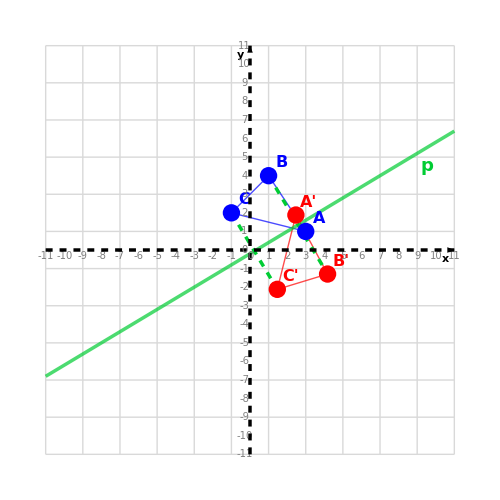

LEGENDA:

• Modré body a čiary: Pôvodný trojuholník

• Červené body a čiary: Trojuholník po symetrii

• Zelené čiara: Os symetrie

• Zelené prerušované čiary: Spojenia zodpovedajúcich si vrcholov

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodné vrcholy (modrá):

Vrchol A: {3,1}

Vrchol B: {1,4}

Vrchol C: {-1,2}

Výsledné vrcholy (červená):

Vrchol A': {42/17,32/17}

Vrchol B': {71/17,-22/17}

Vrchol C': {25/17,-36/17}

MATEMATICKÉ VLASTNOSTI:

• Symetria podľa priamky je izometrická transformácia - zachováva vzdialenosti medzi bodmi

• Symetria zachováva veľkosť a tvar geometrických útvarov

• Symetria zachováva uhly medzi úsečkami a ich dĺžky

• Symetria zachováva obsahy a obvody

• Body ležiace na osi symetrie zostávajú po symetrii nezmenené

• Aplikovaním symetrie dvakrát získame pôvodný obraz - je to transformácia rádu 2

• Spojnica bodu a jeho obrazu je vždy kolmá na os symetrie

• Stred spojnice bodu a jeho obrazu vždy leží na osi symetrie

VÝZNAMNÉ OSI SYMETRIE:

• Os x (y = 0): bod [x, y] sa zobrazí na [x, -y]

• Os y (x = 0): bod [x, y] sa zobrazí na [-x, y]

• Priamka y = x: bod [x, y] sa zobrazí na [y, x]

• Priamka y = -x: bod [x, y] sa zobrazí na [-y, -x]

DRUHÁ TRANSFORMÁCIA: Skosenie

GEOMETRICKÉ TRANSFORMÁCIE TROJUHOLNÍKA - SKOSENIE

========================================

ZADANIE:

Majme trojuholník ABC s vrcholmi:

(42/17 | 32/17
71/17 | -22/17
25/17 | -36/17)

Vykonajte skosenie trojuholníka v 2D priestore v smere osi x s koeficientom k = -3/2 a v smere osi y s koeficientom k = 1.

Transformačná matica skosenia:

(1 | -3/2
1 | 1)

POSTUP:

Pre výpočet použijeme maticu skosenia:

Transformačná matica pre skosenie v smere osí x a y:

(1 | kx
ky | 1)

Vzorec pre výpočet nových súradníc pri skosení v smere osí x a y:

x' = x + kx·y

y' = ky·x + y

Naše hodnoty: kx = -3/2, ky = 1

TEÓRIA MATICOVÉHO ZOBRAZENIA SKOSENIA:

Pri skosení v 2D priestore používame transformačné matice, ktoré umožňujú vyjadriť skosenie ako maticové násobenie:

Obecná transformačná matica skosenia:

(1 | kx
ky | 1)

Ak je bod P = [x, y] v 2D priestore, skosenie môžeme zapísať ako maticové násobenie:

(1 | kx
ky | 1) · (x
y) = (x + kx·y
ky·x + y)

Pre naše hodnoty skosenia:

kx = -3/2 (koeficient skosenia v smere osi x)

ky = 1 (koeficient skosenia v smere osi y)

VÝPOČET SKOSENIA JEDNOTLIVÝCH VRCHOLOV:

VRCHOL A:

Pôvodné súradnice: [42/17, 32/17]

Maticový zápis transformácie bodu A:

(1 | -3/2
1 | 1) |  ·  | (42/17
32/17) |  =  | (-6/17
74/17)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | -3/2 | ] · [ | 42/17 | 32/17 | ]^T = | -6/17

= (1 · 42/17) + (-3/2 · 32/17)

= (1 · 42/17) + (-3/2 · 32/17)

= 42/17 + -48/17

= -6/17

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 1 | 1 | ] · [ | 42/17 | 32/17 | ]^T = | 74/17

= (1 · 42/17) + (1 · 32/17)

= (1 · 42/17) + (1 · 32/17)

= 42/17 + 32/17

= 74/17

Pre skosenie v smere osí x a y:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + kx·y

- Y-ová súradnica sa mení podľa hodnoty X: y' = ky·x + y

Výsledné súradnice bodu A' = [-6/17, 74/17]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + kx·y  =>  42/17 + -3/2·32/17 = -6/17

y' = ky·x + y  =>  1·42/17 + 32/17 = 74/17

Výsledné súradnice vrcholu A':

[-6/17, 74/17]

--------------------------------------------------

VRCHOL B:

Pôvodné súradnice: [71/17, -22/17]

Maticový zápis transformácie bodu B:

(1 | -3/2
1 | 1) |  ·  | (71/17
-22/17) |  =  | (104/17
49/17)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | -3/2 | ] · [ | 71/17 | -22/17 | ]^T = | 104/17

= (1 · 71/17) + (-3/2 · -22/17)

= (1 · 71/17) + (-3/2 · -22/17)

= 71/17 + 33/17

= 104/17

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 1 | 1 | ] · [ | 71/17 | -22/17 | ]^T = | 49/17

= (1 · 71/17) + (1 · -22/17)

= (1 · 71/17) + (1 · -22/17)

= 71/17 + -22/17

= 49/17

Pre skosenie v smere osí x a y:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + kx·y

- Y-ová súradnica sa mení podľa hodnoty X: y' = ky·x + y

Výsledné súradnice bodu B' = [104/17, 49/17]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + kx·y  =>  71/17 + -3/2·-22/17 = 104/17

y' = ky·x + y  =>  1·71/17 + -22/17 = 49/17

Výsledné súradnice vrcholu B':

[104/17, 49/17]

--------------------------------------------------

VRCHOL C:

Pôvodné súradnice: [25/17, -36/17]

Maticový zápis transformácie bodu C:

(1 | -3/2
1 | 1) |  ·  | (25/17
-36/17) |  =  | (79/17
-11/17)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | -3/2 | ] · [ | 25/17 | -36/17 | ]^T = | 79/17

= (1 · 25/17) + (-3/2 · -36/17)

= (1 · 25/17) + (-3/2 · -36/17)

= 25/17 + 54/17

= 79/17

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 1 | 1 | ] · [ | 25/17 | -36/17 | ]^T = | -11/17

= (1 · 25/17) + (1 · -36/17)

= (1 · 25/17) + (1 · -36/17)

= 25/17 + -36/17

= -11/17

Pre skosenie v smere osí x a y:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + kx·y

- Y-ová súradnica sa mení podľa hodnoty X: y' = ky·x + y

Výsledné súradnice bodu C' = [79/17, -11/17]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + kx·y  =>  25/17 + -3/2·-36/17 = 79/17

y' = ky·x + y  =>  1·25/17 + -36/17 = -11/17

Výsledné súradnice vrcholu C':

[79/17, -11/17]

--------------------------------------------------

VÝSLEDOK TRANSFORMÁCIE CELÉHO TROJUHOLNÍKA:

Pôvodný trojuholník ABC:

(42/17 | 32/17
71/17 | -22/17
25/17 | -36/17)

Skosený trojuholník A'B'C':

(-6/17 | 74/17
104/17 | 49/17
79/17 | -11/17)

VIZUALIZÁCIA TRANSFORMÁCIE:

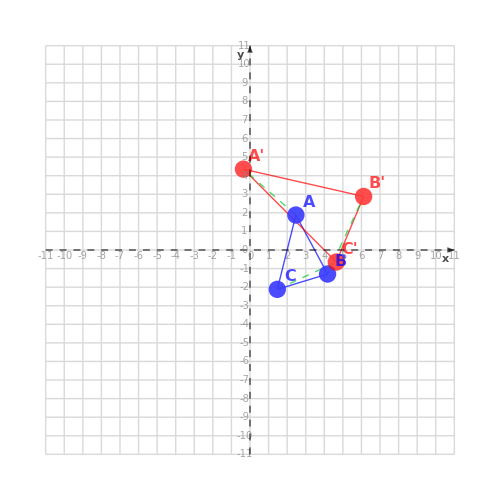

LEGENDA:

• Modré body a čiary: Pôvodný trojuholník

• Červené body a čiary: Skosený trojuholník

• Zelené prerušované čiary: Dráha pohybu vrcholov pri skosení

FAREBNÉ OZNAČENIA V MATICOVÝCH VÝPOČTOCH:

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodné vrcholy (modrá):

Vrchol A: {42/17,32/17}

Vrchol B: {71/17,-22/17}

Vrchol C: {25/17,-36/17}

Výsledné vrcholy (červená):

Vrchol A': {-6/17,74/17}

Vrchol B': {104/17,49/17}

Vrchol C': {79/17,-11/17}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficient skosenia:

kx' = -kx = 3/2 v smere osi x

ky' = -ky = -1 v smere osi y

MATEMATICKÉ VLASTNOSTI:

• Skosenie je lineárna transformácia, ktorá zachováva rovnobežnosť priamok s jednou z osí

• Pri skosení v smere osí x a y sa menia obe súradnice bodov

• Skosením v smere osí x a y sa priamky rovnobežné s oboma osami deformujú

• Skosenie mení uhly a tvary geometrických útvarov, ale zachováva ich obsah

• Body ležiace na osi, ktorá je rovnobežná so smerom skosenia, sa nemenia

• Skosenie je afínna transformácia, ktorá nezachováva vzdialenosti ani uhly

ŠPECIÁLNE PRÍPADY:

• Pre k = 0 je skosenie identickou transformáciou (bod sa nemení)

• Pre veľké hodnoty |k| sa útvar výrazne skosí a môže byť ťažšie rozpoznateľný

• Pre k = 1 sa vytvorí rovnoramenný pravouhlý trojuholník z pôvodného štvorca

• Pre k = -1 sa vytvorí rovnoramenný pravouhlý trojuholník z pôvodného štvorca (v opačnom smere)

TRETIA TRANSFORMÁCIA: Zväčšenie/Zmenšenie

GEOMETRICKÉ TRANSFORMÁCIE TROJUHOLNÍKA - ZVÄČŠENIE/ZMENŠENIE

========================================

ZADANIE:

Majme trojuholník ABC s vrcholmi:

(-6/17 | 74/17
104/17 | 49/17
79/17 | -11/17)

Vykonajte zväčšenie v smere osi x trojuholníka pomocou transformačnej matice v 2D priestore:

(3/2 | 0
0 | 1)

TEÓRIA MATICOVÉHO ZOBRAZENIA ZVÄČŠENIA/ZMENŠENIA:

Pri zväčšení/zmenšení v 2D priestore používame maticové násobenie, ktoré umožňuje zmeniť veľkosť objektu nezávisle v smere osí x a y:

Transformačná matica zväčšenia/zmenšenia:

(sx | 0
0 | sy)

Ak je bod P = [x, y] v základných súradniciach, zväčšenie/zmenšenie môžeme zapísať ako maticové násobenie:

(sx | 0
0 | sy) · (x
y) = (x·sx
y·sy)

Pre naše hodnoty:

sx = 3/2 (zväčšovanie v smere osi x)

sy = 1 (zmenšovanie v smere osi y)

VÝPOČET TRANSFORMÁCIE JEDNOTLIVÝCH VRCHOLOV:

VRCHOL A:

Pôvodné súradnice: [-6/17, 74/17]

Maticový zápis transformácie bodu A:

(3/2 | 0
0 | 1) |  ·  | (-6/17
74/17) |  =  | (-9/17
74/17)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 3/2 | 0 | ] · [ | -6/17 | 74/17 | ]^T = | -9/17

= (3/2 · -6/17) + (0 · 74/17)

= -9/17 + 0

= -9/17

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | -6/17 | 74/17 | ]^T = | 74/17

= (0 · -6/17) + (1 · 74/17)

= 0 + 74/17

= 74/17

Výsledná reprezentácia bodu A':

[-9/17, 74/17]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  -6/17 · 3/2 = -9/17

y' = y·sy  =>  74/17 · 1 = 74/17

Výsledné súradnice vrcholu A':

[-9/17, 74/17]

--------------------------------------------------

VRCHOL B:

Pôvodné súradnice: [104/17, 49/17]

Maticový zápis transformácie bodu B:

(3/2 | 0
0 | 1) |  ·  | (104/17
49/17) |  =  | (156/17
49/17)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 3/2 | 0 | ] · [ | 104/17 | 49/17 | ]^T = | 156/17

= (3/2 · 104/17) + (0 · 49/17)

= 156/17 + 0

= 156/17

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | 104/17 | 49/17 | ]^T = | 49/17

= (0 · 104/17) + (1 · 49/17)

= 0 + 49/17

= 49/17

Výsledná reprezentácia bodu B':

[156/17, 49/17]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  104/17 · 3/2 = 156/17

y' = y·sy  =>  49/17 · 1 = 49/17

Výsledné súradnice vrcholu B':

[156/17, 49/17]

--------------------------------------------------

VRCHOL C:

Pôvodné súradnice: [79/17, -11/17]

Maticový zápis transformácie bodu C:

(3/2 | 0
0 | 1) |  ·  | (79/17
-11/17) |  =  | (237/34
-11/17)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 3/2 | 0 | ] · [ | 79/17 | -11/17 | ]^T = | 237/34

= (3/2 · 79/17) + (0 · -11/17)

= 237/34 + 0

= 237/34

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | 79/17 | -11/17 | ]^T = | -11/17

= (0 · 79/17) + (1 · -11/17)

= 0 + -11/17

= -11/17

Výsledná reprezentácia bodu C':

[237/34, -11/17]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  79/17 · 3/2 = 237/34

y' = y·sy  =>  -11/17 · 1 = -11/17

Výsledné súradnice vrcholu C':

[237/34, -11/17]

--------------------------------------------------

VÝSLEDOK TRANSFORMÁCIE CELÉHO TROJUHOLNÍKA:

Pôvodný trojuholník ABC:

(-6/17 | 74/17
104/17 | 49/17
79/17 | -11/17)

Transformovaný trojuholník A'B'C':

(-9/17 | 74/17
156/17 | 49/17
237/34 | -11/17)

VIZUALIZÁCIA TRANSFORMÁCIE:

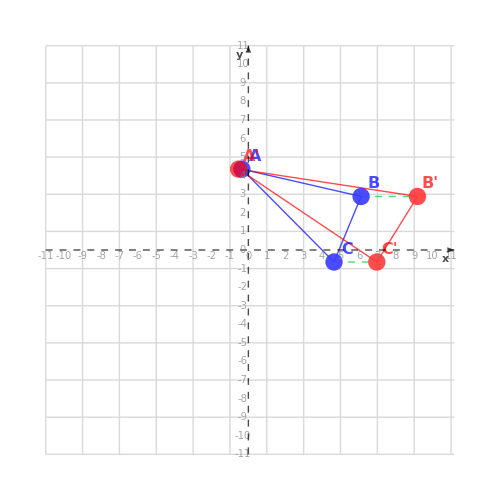

LEGENDA:

• Modré body a čiary: Pôvodný trojuholník

• Červené body a čiary: Transformovaný trojuholník

• Zelené prerušované čiary: Dráha zmeny veľkosti vrcholov

FAREBNÉ OZNAČENIA V MATICOVÝCH VÝPOČTOCH:

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodné vrcholy (modrá):

Vrchol A: {-6/17,74/17}

Vrchol B: {104/17,49/17}

Vrchol C: {79/17,-11/17}

Výsledné vrcholy (červená):

Vrchol A': {-9/17,74/17}

Vrchol B': {156/17,49/17}

Vrchol C': {237/34,-11/17}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficienty:

sx' = 1/sx = 2/3 (zmenšovanie v smere osi x)

sy' = 1/sy = 1 (zmenšovanie v smere osi y)

MATEMATICKÉ VLASTNOSTI:

• Pri rôznych koeficientoch (sx = 3/2, sy = 1):

- Mení sa tvar (podobnosť) geometrických útvarov

- Uhly medzi úsečkami sa menia

- Pomer dĺžok úsečiek sa mení v závislosti od ich smeru

- Obsah trojuholníka sa zväčší 3/2-krát

• Nemení sa poloha počiatku súradnicovej sústavy [0,0]

• Body, ktoré ležia na osi x, zostanú ležať na osi x (ich y-ová súradnica zostáva nulová)

• Body, ktoré ležia na osi y, zostanú ležať na osi y (ich x-ová súradnica zostáva nulová)

POSTUPNÝ VÝPOČET:

Pôvodný trojuholník ABC:

Vrcholy:

(3 | 1
1 | 4
-1 | 2)

Vlastnosti trojuholníka:

Obsah: 5

Obvod: 11

Po prvej transformácii (Symetria):

Vrcholy trojuholníka A'B'C':

(42/17 | 32/17
71/17 | -22/17
25/17 | -36/17)

Vlastnosti trojuholníka:

Obsah: 5

Obvod: 11

Po druhej transformácii (Skosenie):

Vrcholy trojuholníka A''B''C'':

(-6/17 | 74/17
104/17 | 49/17
79/17 | -11/17)

Vlastnosti trojuholníka:

Obsah: 12

Obvod: 18

Po tretej transformácii (Zväčšenie/Zmenšenie):

Vrcholy trojuholníka A'''B'''C''':

(-9/17 | 74/17
156/17 | 49/17
237/34 | -11/17)

Vlastnosti trojuholníka:

Obsah: 19

Obvod: 23

VÝPOČET SÚHRNNEJ TRANSFORMAČNEJ MATICE:

Transformačné matice pre jednotlivé transformácie:

Matica pre Symetria (M1):

(8/17 | 15/17 | 3/17
15/17 | -8/17 | -5/17
0 | 0 | 1)

Matica pre Skosenie (M2):

(1 | -3/2 | 0
1 | 1 | 0
0 | 0 | 1)

Matica pre Zväčšenie/Zmenšenie (M3):

(3/2 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Postupný výpočet súhrnnej matice:

Krok 1: Začíname s maticou prvej transformácie:

M₁ = Matica pre Symetria

(8/17 | 15/17 | 3/17
15/17 | -8/17 | -5/17
0 | 0 | 1)

Krok 2: Násobenie matíc

Pri kompozícii transformácií násobíme matice v opačnom poradí, ako sa aplikujú.

Matica pre aktuálnu transformáciu sa násobí s výsledkom predchádzajúcich transformácií.

M2 · M₁ = Matica pre Skosenie · Matica pre Symetria

Matica pre Skosenie (M2):

(1 | -3/2 | 0
1 | 1 | 0
0 | 0 | 1)

Matica prvej transformácie (M₁):

(8/17 | 15/17 | 3/17
15/17 | -8/17 | -5/17
0 | 0 | 1)

Výpočet násobenia matíc:

C[1,1] = {(1 × 8/17) + ,(-3/2 × 15/17) + ,(0 × 0)} = -29/34

C[1,2] = {(1 × 15/17) + ,(-3/2 × -8/17) + ,(0 × 0)} = 27/17

C[1,3] = {(1 × 3/17) + ,(-3/2 × -5/17) + ,(0 × 1)} = 21/34

C[2,1] = {(1 × 8/17) + ,(1 × 15/17) + ,(0 × 0)} = 23/17

C[2,2] = {(1 × 15/17) + ,(1 × -8/17) + ,(0 × 0)} = 7/17

C[2,3] = {(1 × 3/17) + ,(1 × -5/17) + ,(0 × 1)} = -2/17

C[3,1] = {(0 × 8/17) + ,(0 × 15/17) + ,(1 × 0)} = 0

C[3,2] = {(0 × 15/17) + ,(0 × -8/17) + ,(1 × 0)} = 0

C[3,3] = {(0 × 3/17) + ,(0 × -5/17) + ,(1 × 1)} = 1

Výsledok násobenia:

(-29/34 | 27/17 | 21/34
23/17 | 7/17 | -2/17
0 | 0 | 1)

Krok 3: Násobenie matíc

M3 · (M2 · ... · M₁) = Matica pre Zväčšenie/Zmenšenie · Výsledok predchádzajúcich transformácií (M2 · ... · M₁)

Matica pre Zväčšenie/Zmenšenie (M3):

(3/2 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Výsledok predchádzajúcich transformácií (M2 · ... · M₁):

(-29/34 | 27/17 | 21/34
23/17 | 7/17 | -2/17
0 | 0 | 1)

Výpočet násobenia matíc:

C[1,1] = {(3/2 × -29/34) + ,(0 × 23/17) + ,(0 × 0)} = -87/68

C[1,2] = {(3/2 × 27/17) + ,(0 × 7/17) + ,(0 × 0)} = 81/34

C[1,3] = {(3/2 × 21/34) + ,(0 × -2/17) + ,(0 × 1)} = 63/68

C[2,1] = {(0 × -29/34) + ,(1 × 23/17) + ,(0 × 0)} = 23/17

C[2,2] = {(0 × 27/17) + ,(1 × 7/17) + ,(0 × 0)} = 7/17

C[2,3] = {(0 × 21/34) + ,(1 × -2/17) + ,(0 × 1)} = -2/17

C[3,1] = {(0 × -29/34) + ,(0 × 23/17) + ,(1 × 0)} = 0

C[3,2] = {(0 × 27/17) + ,(0 × 7/17) + ,(1 × 0)} = 0

C[3,3] = {(0 × 21/34) + ,(0 × -2/17) + ,(1 × 1)} = 1

Výsledok násobenia:

(-87/68 | 81/34 | 63/68
23/17 | 7/17 | -2/17
0 | 0 | 1)

VÝSLEDNÁ SÚHRNNÁ TRANSFORMAČNÁ MATICA:

(-87/68 | 81/34 | 63/68
23/17 | 7/17 | -2/17
0 | 0 | 1)

APLIKÁCIA SÚHRNNEJ MATICE NA PÔVODNÝ TROJUHOLNÍK:

Súhrnná transformačná matica:

(-87/68 | 81/34 | 63/68
23/17 | 7/17 | -2/17
0 | 0 | 1)

Pôvodný trojuholník ABC:

| x | y
A | 3 | 1
B | 1 | 4
C | -1 | 2

Postup pri aplikovaní súhrnnej transformačnej matice na trojuholník:

1. Každý vrchol (x, y) sa rozšíri na homogénne súradnice (x, y, 1)

2. Vynásobí sa súhrnnou transformačnou maticou 3×3

3. Z výsledného vektora vezmeme prvé dve súradnice, čím dostaneme transformovaný vrchol

PODROBNÝ VÝPOČET PRE KAŽDÝ VRCHOL:

Vrchol A:

Pôvodné súradnice: {3,1}

V homogénnych súradniciach: {3,1,1}

Maticové násobenie:

M · A =

(-87/68 | 81/34 | 63/68
23/17 | 7/17 | -2/17
0 | 0 | 1) · (3
1
1)

Podrobný výpočet:

Riadok 1:

-87/68 · 3 + 81/34 · 1 + 63/68 · 1 = -9/17

Riadok 2:

23/17 · 3 + 7/17 · 1 + -2/17 · 1 = 74/17

Riadok 3:

0 · 3 + 0 · 1 + 1 · 1 = 1

Výsledok pre vrchol A:

V homogénnych súradniciach: {-9/17,74/17,1}

Transformované súradnice (A'): {-9/17,74/17}

Očakávaný výsledok (A'): {-9/17,74/17}

✓ Výsledok sa zhoduje s očakávaným bodom.

Vrchol B:

Pôvodné súradnice: {1,4}

V homogénnych súradniciach: {1,4,1}

Maticové násobenie:

M · B =

(-87/68 | 81/34 | 63/68
23/17 | 7/17 | -2/17
0 | 0 | 1) · (1
4
1)

Podrobný výpočet:

Riadok 1:

-87/68 · 1 + 81/34 · 4 + 63/68 · 1 = 156/17

Riadok 2:

23/17 · 1 + 7/17 · 4 + -2/17 · 1 = 49/17

Riadok 3:

0 · 1 + 0 · 4 + 1 · 1 = 1

Výsledok pre vrchol B:

V homogénnych súradniciach: {156/17,49/17,1}

Transformované súradnice (B'): {156/17,49/17}

Očakávaný výsledok (B'): {156/17,49/17}

✓ Výsledok sa zhoduje s očakávaným bodom.

Vrchol C:

Pôvodné súradnice: {-1,2}

V homogénnych súradniciach: {-1,2,1}

Maticové násobenie:

M · C =

(-87/68 | 81/34 | 63/68
23/17 | 7/17 | -2/17
0 | 0 | 1) · (-1
2
1)

Podrobný výpočet:

Riadok 1:

-87/68 · -1 + 81/34 · 2 + 63/68 · 1 = 237/34

Riadok 2:

23/17 · -1 + 7/17 · 2 + -2/17 · 1 = -11/17

Riadok 3:

0 · -1 + 0 · 2 + 1 · 1 = 1

Výsledok pre vrchol C:

V homogénnych súradniciach: {237/34,-11/17,1}

Transformované súradnice (C'): {237/34,-11/17}

Očakávaný výsledok (C'): {237/34,-11/17}

✓ Výsledok sa zhoduje s očakávaným bodom.

VÝSLEDNÝ TRANSFORMOVANÝ TROJUHOLNÍK A'B'C':

| x | y
A' | -9/17 | 74/17
B' | 156/17 | 49/17
C' | 237/34 | -11/17

Očakávaný výsledný trojuholník:

| x | y
A' | -9/17 | 74/17
B' | 156/17 | 49/17
C' | 237/34 | -11/17

✓ OVERENIE ÚSPEŠNÉ: Transformácia pomocou súhrnnej matice dáva správny výsledok.

ZÁVER:

Použitím jedinej transformácie definovanej súhrnnou maticou sme dosiahli rovnaký výsledok,

ako postupným aplikovaním viacerých transformácií. Tento princíp je kľúčový

v počítačovej grafike a umožňuje efektívne vykresľovanie zložitých transformácií.

SÚHRNNÁ VIZUALIZÁCIA:

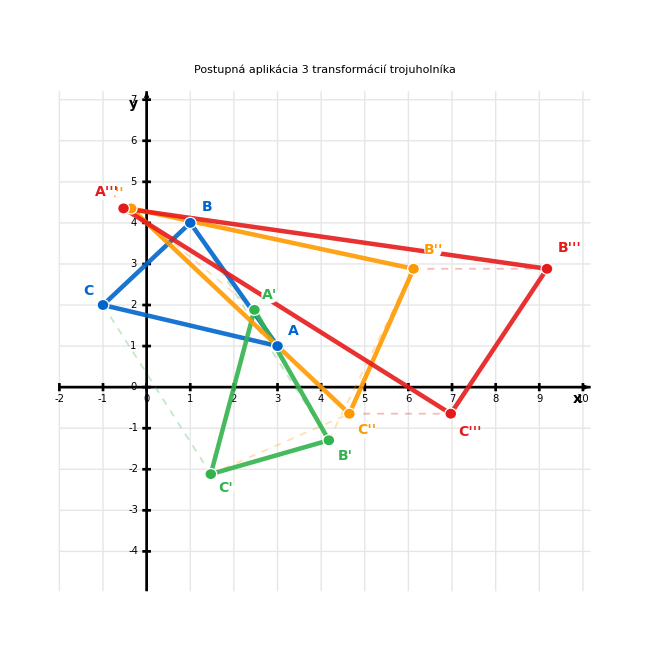

LEGENDA:

• Modré body a čiary: Pôvodný trojuholník ABC

• Tmavozelené body a čiary: Trojuholník po prvej transformácii (Symetria)

• Oranžové body a čiary: Trojuholník po druhej transformácii (Skosenie)

• Červené body a čiary: Trojuholník po tretej transformácii (Zväčšenie/Zmenšenie)

Postupnosť transformácií:

1. Symetria podľa priamky 3x -5y -1 = 0

2. Skosenie s parametrami {-1.5, 1}

3. Zväčšenie/Zmenšenie s parametrami {3/2, 1}

{{{3,1},{1,4},{-1,2}},{{{3,1},{1,4},{-1,2}},{{42/17,32/17},{71/17,-22/17},{25/17,-36/17}},{{-0.352941,74/17},{6.11765,49/17},{4.64706,-11/17}},{{-56768062529881/107228562556442,74/17},{156/17,49/17},{237/34,-11/17}}},{Symetria,Skosenie,Zväčšenie/Zmenšenie},Hard,{{3,-5,-1},{-1.5,1},{3/2,1}}}

```mathematica
TrojuholnikTrojitaTransformacia[]
```